```mathematica
Quit[];
```

```mathematica
SetOptions[EvaluationNotebook[],ShowGroupOpener->True]
```

## Load packages (run this)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$LoadFeynArts=True;
Global`$LoadAddOns={"FeynHelpers"};
<<FeynCalc`;
$FAVerbose = 0;

FAPatch[PatchModelsOnly->True];
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

args::shdw: Symbol args appears in multiple contexts {FeynArts`,Global`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

FeynHelpers 1.1.0 loaded.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

Patching FeynArts models... done!

## Diagram and amplitude utilities (run this)

### Scalar products

```mathematica
setDMSPs[]:=Module[{},
SP[px,px]=mx^2;
SP[pxbar,pxbar]=mx^2;
SP[px,pxbar]=Ecm^2/2-mx^2;
]
```

```mathematica
setTwoBodyFSSPs[mFS_]:=Module[{},
setDMSPs[];

SP[p1,p1]=mFS^2;
SP[p2,p2]=mFS^2;

SP[p1,p2]=s/2-mFS^2;

SP[p1,px]=(mFS^2+mx^2-t)/2;
SP[p2,pxbar]=(mFS^2+mx^2-t)/2;

SP[p2,px]=(mFS^2+mx^2-u)/2;
SP[p1,pxbar]=(mFS^2+mx^2-u)/2;
]
```

### Functions for generating diagrams

```mathematica
(*exclusions=Join[{V[1],V[2],V[3],V[4]},mesonList];*)
exclusions={V[1],V[2],V[3](*,V[4]*)};

frModelName="EFT_MeV_DM_vector_no_contact";
model={frModelName<>"/"<>frModelName};
genericModel={"Lorentz",frModelName<>"/"<>frModelName};

insertionLevel={Particles};
```

```mathematica
genDiags[inFields_,outFields_,nLoops_:0,adj_:{3,4,5},otherExclusions_:{}]:=Block[{tops},
tops=CreateTopologies[nLoops, Length[inFields]-> Length[outFields],ExcludeTopologies-> {Tadpoles,SelfEnergies,WFCorrections},Adjacencies-> adj];
InsertFields[tops,inFields-> outFields,InsertionLevel-> insertionLevel,Model-> model,GenericModel-> genericModel,ExcludeParticles-> Join[exclusions,otherExclusions]]
]
```

### Abbreviations for states

```mathematica
stateπ0=S[1];
stateπm=S[2];
stateπp=-S[2];
statek0=S[3];
statek0bar=-S[3];
statekm=S[4];
statekp=-S[4];
stateη=S[5];
stateγ=V[1];
stateρ=V[2];
stateω=V[3];
statev=V[4];
stateν=F[1];
stateνbar=-F[1];
statel=F[2];
statelbar=-F[2];
statex=F[3];
statexbar=-F[3];

mesonList={stateπ0,stateπp,stateπm,statekp,statekm,statek0,statek0bar,stateη};
```

### Function for creating amplitudes

Photon momentum should always be k

```mathematica
createAmp[diags_,inmomenta_,outmomenta_,lorentzIndices_,truncated_:False]:=Module[{amp},
(*Compute the diagram*)
amp=CreateFeynAmp[diags, PreFactor->-ⅈ,Truncated-> truncated,GaugeRules->{}];
amp=FCFAConvert[amp,
IncomingMomenta-> inmomenta,
OutgoingMomenta-> outmomenta,
LorentzIndexNames-> lorentzIndices,
LoopMomenta->{l}, 
UndoChiralSplittings->True,
List->False,
SMP-> True,
ChangeDimension-> 4,
FinalSubstitutions-> M$FACouplings,
TransversePolarizationVectors->{k}];

Simplify[ExpandScalarProduct[DiracSimplify[Contract[amp],DiracSubstitute67-> True]]]
]
```

### Hacky way to drop extra V diagrams

```mathematica
dropExtraVs[amp_]:=amp/.{gvuu->gvCounter gvuu,gvdd->gvCounter gvdd,gvss->gvCounter gvss}//Coefficient[#,gvCounter]&
```

### For writing to python files

```mathematica
dotProdsToStrings[expr_]:=expr//ReplaceAll[#,Pair[Momentum[pA_], Momentum[pB_]]:>ToExpression[ToString[pA]<>"DOT"<>ToString[pB]]]&
```

```mathematica
pyDir=NotebookDirectory[]<>"/python/";
```

### Compute 2→2 cross section

```mathematica
xSecPrefactor[mA_]:=1/((2 Ecm/2)^2 2(√(Ecm^2/4-mA^2)/√(Ecm^2/4)))
```

This function computes the cross section by integrating over cos θ

```mathematica
getXSec[amp_,mIn_,m1_,m2_]:=1/(16π)(2pOut)/(√s) xSecPrefactor[mIn] Integrate[amp/.t->m1^2+mx^2-2(1/2 √(s(pOut^2+m1^2))-pOut √(s/4-mx^2)cθ),{cθ,-1,1}]/.{pOut->(√(s^2+(m1^2-m2^2)^2-2 s (m1^2+m2^2)))/(2 √s)}//Simplify
```

This function computes the cross section by integrating over t, under the assumption that the final state particles’ masses are idential.

For the case m_1=m_2=m:
	dt/dc_θ=1/2 √((s-4 m^2)(s-4 m_x^2))
	⇒∫ dc_θ f(c_θ) = ∫ dt dc_θ/dt f(t) = (2[(s-4 m^2)(s-4 m_x^2)])^(-1/2)∫ dt f(t)
The bounds on t are
	m_x^2+m^2-1/2(s+√((s-4 m^2)(s-4 m_x^2))), m_x^2+m^2+1/2(√((s-4 m^2)(s-4 m_x^2))-s)

```mathematica
getXSecTIntegral[amp_,mIn_,m_]:=Module[{prefactor,tInt,tMin,tMax},
prefactor=1/(16π)(√(s-4 m^2))/(√s) xSecPrefactor[mIn] ;

tMin=m^2+mIn^2-s/2-1/2 √((-4 m^2+s) (-4 mIn^2+s));
tMax=m^2+mIn^2+1/2 (-s+√((-4 m^2+s) (-4 mIn^2+s)));

tInt=Integrate[amp,t];

prefactor((tInt/.t->tMax)-(tInt/.t->tMin))//Simplify
]
```

### Substitute in for unstable mediator propagator

```mathematica
substituteUnstableVPropagator[expr_,moms_]:=expr/.FeynAmpDenominator[PropagatorDenominator[Total[Momentum/@moms], mv]]:>1/(SP[Total[Momentum/@moms]]-mv^2+ⅈ widthv mv)//ScalarProductExpand
```

### Determine integration bounds for t

```mathematica
integrationBoundsT[s_,m1_,m2_,m3_,M_]:=Module[{termA,termB,result},termA = (m2-m3) (m2+m3) (m1-M) (m1+M)+(m1^2+m2^2+m3^2+M^2) s-s^2;
	termB = Sqrt[m2^4+(m3^2-s)^2-2 m2^2 (m3^2+s)] Sqrt[m1^4+(M^2-s)^2-2 m1^2 (M^2+s)];

result = {1/(2 s) (termA - termB), 1/(2 s) (termA + termB)}//Simplify[#,Assumptions->{s>M^2>0}]&
]
```

### Width prefactor

```mathematica
widthFactor[m1_,m2_]:=1/(2mv)(4π)/(16 π^2)1/mv(p/.Solve[√(p^2+m1^2)+√(p^2+m2^2)==mv,p]//Simplify[Abs[#]⟦1⟧,Assumptions->{p>0,m1+m2<mv,mv>0,m1>=0,m2>=0}]&)

widthFactor[m_]:=widthFactor[m,m]
```

# χ̄ χ→A

## χ̄ χ→π^+ π^-

```mathematica
twoMesonFSs={{stateπp,stateπm}(*,{statekp,statekm},{statek0,statek0bar}*)};
```

```mathematica
ClearScalarProducts[];

ampSquaredxbarxtoππ=Module[{fs,diags,amp,ampSquared},
fs={stateπp,stateπm};

ClearScalarProducts[];
setTwoBodyFSSPs[mpi];

diags=genDiags[{statexbar,statex},fs];
amp=createAmp[diags,{pxbar,px},{p1,p2},{μ,ν}]//substituteUnstableVPropagator[#,{p1,p2}]&;

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]];
ampSquared=ampSquared//FermionSpinSum[#,ExtraFactor->1/4]&//ReplaceAll[#,DiracTrace->Tr]&;
ampSquared/.u->2(mpi^2+mx^2)-s-t//Simplify
]
```

-(gvxx^2 (gvdd-gvuu)^2 (Ecm^2 (4 mpi^2-s)+(-2 mpi^2-2 mx^2+s+2 t)^2))/(2 (mv^4+mv^2 (widthv^2-2 s)+s^2))

```mathematica
xSecxbarxtoππ=getXSec[ampSquaredxbarxtoππ,mx,mpi,mpi]/.s->Ecm^2//Simplify[#,Assumptions->{Ecm>mpi0,Ecm^2>mpi0^2}]&
```

(gvxx^2 (Ecm^2-4 mpi^2)^(3/2) (Ecm^2+2 mx^2) (gvdd-gvuu)^2)/(48 π Ecm^2 √(Ecm^2-4 mx^2) (Ecm^4-2 Ecm^2 mv^2+mv^4+mv^2 widthv^2))

```mathematica
(*FortranForm[xSecxbarxtoππ/.Ecm->Q]>>(pyDir<>"xsec_xx_v_pipi.py")*)
```

## χ̄ χ→π^0 γ

```mathematica
threeMesonγFSs={(*{stateγ,stateη},
{stateγ,stateη,statek0,statek0bar},
{stateγ,stateη,statekp,statekm},
{stateγ,stateη,stateπp,stateπm},
{stateγ,statek0,statek0bar,stateπ0},
{stateγ,statek0,statekm,stateπp},
{stateγ,statek0bar,statekp,stateπm},
{stateγ,statekp,statekm,stateπ0},*)
{stateπ0,stateγ},
{stateπ0,stateπp,stateπm,stateγ}};
```

```mathematica
ClearScalarProducts[];

ampSquaredxbarxtoπ0γ=Module[{fs,mMes1,mMes2,mMes3,diags,amp,ampSquared},
fs={stateπ0,stateγ};

(* Set scalar products *)
ClearScalarProducts[];
setDMSPs[];
SP[p,p]=mpi0^2;
SP[k,k]=0;
(* Use Mandelstam vars *)
SP[p,px]=(mx^2+mpi0^2-t)/2;
SP[k,pxbar]=(mx^2-t)/2;
SP[k,px]=(mx^2-u)/2;
SP[p,pxbar]=(mx^2+mpi0^2-u)/2;
SP[k,p]=(s-mpi0^2)/2;

diags=genDiags[{statexbar,statex},fs];

(*Paint[diags,ColumnsXRows->1,ImageSize->{200,200}];*)

amp=createAmp[diags,{pxbar,px},{p,k},{μ,ν}]//substituteUnstableVPropagator[#,{p,k}]&//PropagatorDenominatorExplicit//dropExtraVs;
(* Replace the ϵ symbol *)
amp=amp/.{FALeviCivita->Eps,FAFourVector->Momentum};

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]];
ampSquared=ampSquared//FermionSpinSum[#,ExtraFactor->1/4]&//ReplaceAll[#,DiracTrace->Tr]&//DoPolarizationSums[#,k,0]&;

ampSquared//Contract//ReplaceAll[#,{u->2 mx^2+mpi0^2-s-t}]&//Simplify
]
```

(gvxx^2 qe^2 (gvdd+2 gvuu)^2 (mpi0^4 (2 mx^2+s)-2 mpi0^2 s (mx^2+s+t)+s (2 mx^4-4 mx^2 t+s^2+2 s t+2 t^2)))/(576 π^4 fpi^2 (mv^4+mv^2 (widthv^2-2 s)+s^2))

```mathematica
getXSec[ampSquaredxbarxtoπ0γ,mx,0,mpi0];

xSecxbarxtoπ0γ=%/.s->Ecm^2//Simplify[#,Assumptions->{Ecm>mpi0,Ecm^2>mpi0^2}]&
```

(gvxx^2 qe^2 (Ecm^2-mpi0^2)^3 (Ecm^2+2 mx^2) (gvdd+2 gvuu)^2)/(13824 π^5 Ecm^3 fpi^2 √(Ecm^2-4 mx^2) (Ecm^4-2 Ecm^2 mv^2+mv^4+mv^2 widthv^2))

```mathematica
(*FortranForm[xSecxbarxtoπ0γ/.Ecm->Q]>>(pyDir<>"xsec_xx_v_pi0g.py");*)
```

## χ̄ χ→π^0 V

```mathematica
ClearScalarProducts[];

ampSquaredxbarxtoπ0v=Module[{fs,mMes1,mMes2,mMes3,diags,amp,ampSquared},
fs={stateπ0,statev};

(* Set scalar products *)
ClearScalarProducts[];
setDMSPs[];
SP[p,p]=mpi0^2;
SP[k,k]=mv^2;
(* Use Mandelstam vars *)
SP[p,px]=(mx^2+mpi0^2-t)/2;
SP[k,pxbar]=(mx^2+mv^2-t)/2;
SP[k,px]=(mx^2+mv^2-u)/2;
SP[p,pxbar]=(mx^2+mpi0^2-u)/2;
SP[k,p]=(s-(mv^2+mpi0^2))/2;

diags=genDiags[{statexbar,statex},fs];

(*Paint[diags,ColumnsXRows->1,ImageSize->{200,200}];*)

amp=createAmp[diags,{pxbar,px},{p,k},{μ,ν}]//substituteUnstableVPropagator[#,{p,k}]&//PropagatorDenominatorExplicit;
(* Replace the ϵ symbol *)
amp=amp/.{FALeviCivita->Eps,FAFourVector->Momentum};

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]];
ampSquared=ampSquared//FermionSpinSum[#,ExtraFactor->1/4]&//ReplaceAll[#,DiracTrace->Tr]&//DoPolarizationSums[#,k]&;

ampSquared//Contract//ReplaceAll[#,{u->2 mx^2+mv^2+mpi0^2-s-t}]&//Simplify
]
```

(gvxx^2 (gvdd^2-gvuu^2)^2 (mpi0^4 (2 mx^2+s)-2 mpi0^2 (2 mv^2 mx^2+s (mx^2+s+t))+mv^4 (2 mx^2+s)-2 mv^2 s (mx^2+s+t)+s (2 mx^4-4 mx^2 t+s^2+2 s t+2 t^2)))/(64 π^4 fpi^2 (mv^4+mv^2 (widthv^2-2 s)+s^2))

```mathematica
getXSec[ampSquaredxbarxtoπ0v,mx,mv,mpi0];

xSecxbarxtoπ0v=%/.s->Ecm^2//Simplify[#,Assumptions->{Ecm>mpi0+mv>0,mv>0,mpi0>0}]&
```

(gvxx^2 (Ecm^2+2 mx^2) (gvdd-gvuu)^2 (gvdd+gvuu)^2 (Ecm^4-2 Ecm^2 (mpi0^2+mv^2)+(mpi0^2-mv^2)^2)^(3/2))/(1536 π^5 Ecm^3 fpi^2 √(Ecm^2-4 mx^2) (Ecm^4-2 Ecm^2 mv^2+mv^4+mv^2 widthv^2))

```mathematica
getXSec[ampSquaredxbarxtoπ0v,mx,mv,mpi0];

xSecxbarxtoπ0v=%/.s->Ecm^2//FullSimplify[#,Assumptions->{Ecm>mpi0+mv>0,mv>0,mpi0>0}]&
```

(gvxx^2 (Ecm^2+2 mx^2) (gvdd-gvuu)^2 (gvdd+gvuu)^2 ((Ecm-mpi0-mv) (Ecm+mpi0-mv) (Ecm-mpi0+mv) (Ecm+mpi0+mv))^(3/2))/(1536 π^5 Ecm^3 fpi^2 √(Ecm^2-4 mx^2) ((Ecm^2-mv^2)^2+mv^2 widthv^2))

```mathematica
FortranForm[xSecxbarxtoπ0v/.Ecm->Q]>>(pyDir<>"xsec_xx_v_pi0v.py");
```

## χ̄ χ→π^+ π^- γ

```mathematica
twoMesonγFSs={{stateπp,stateπm,stateγ}(*,{statekp,statekm,stateγ}*)};
```

Compute ℳ_(V^*→π^+π^-γ)

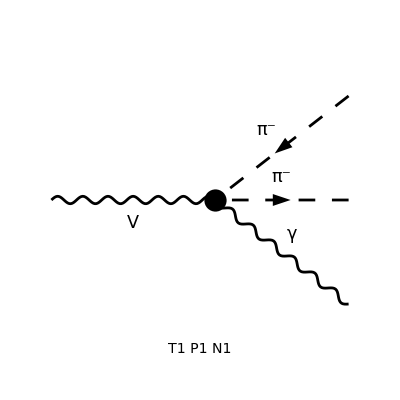

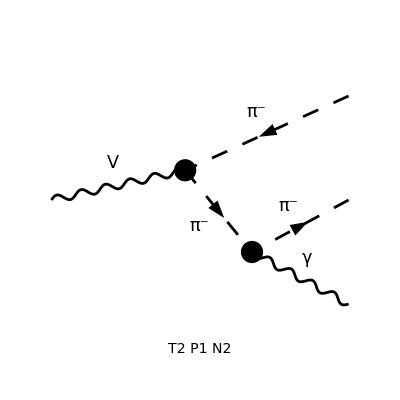

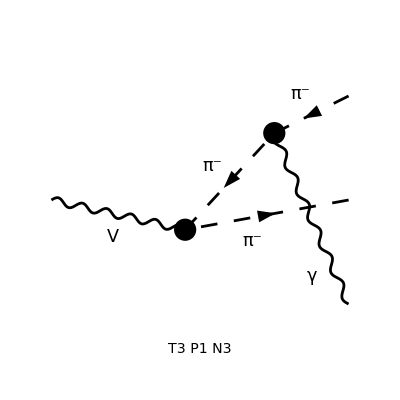

{qe (-(gvdd-gvuu)) ((ε̄)^*)^α(k) (2 (ḡ)^αμ-(((k̄)^α+2 OverBar[p1]^α) ((k̄)^μ+OverBar[p1]^μ-OverBar[p2]^μ))/(2 (k̄·OverBar[p1]))-(((k̄)^α+2 OverBar[p2]^α) ((k̄)^μ-OverBar[p1]^μ+OverBar[p2]^μ))/(2 (k̄·OverBar[p2]))),-1/((k̄·OverBar[p1])^2 (k̄·OverBar[p2])^2)qe^2 (gvdd-gvuu)^2 (4 (ḡ)^μν (k̄·OverBar[p1])^2 (k̄·OverBar[p2])^2+mpi^2 (k̄)^ν OverBar[p2]^μ (k̄·OverBar[p1])^2-mpi^2 OverBar[p1]^ν OverBar[p2]^μ (k̄·OverBar[p1])^2+mpi^2 OverBar[p2]^μ OverBar[p2]^ν (k̄·OverBar[p1])^2-mpi^2 OverBar[p1]^ν OverBar[p2]^μ (k̄·OverBar[p2])^2+(k̄)^μ (OverBar[p2]^ν ((mpi^2-2 (k̄·OverBar[p2])) (k̄·OverBar[p1])^2-mpi^2 (k̄·OverBar[p2])^2)+OverBar[p1]^ν (-mpi^2 (k̄·OverBar[p1])^2+mpi^2 (k̄·OverBar[p2])^2-2 (k̄·OverBar[p1]) (k̄·OverBar[p2])^2)+(k̄)^ν (mpi^2 (k̄·OverBar[p1])^2+mpi^2 (k̄·OverBar[p2])^2+2 (k̄·OverBar[p1]) (k̄·OverBar[p2]) (OverBar[p1]·OverBar[p2])))+OverBar[p1]^μ ((k̄)^ν (-mpi^2 (k̄·OverBar[p1])^2+mpi^2 (k̄·OverBar[p2])^2-2 (k̄·OverBar[p1]) (k̄·OverBar[p2])^2)+OverBar[p2]^ν (-(mpi^2-2 (k̄·OverBar[p2])) (k̄·OverBar[p1])^2-mpi^2 (k̄·OverBar[p2])^2+2 (k̄·OverBar[p1]) (k̄·OverBar[p2]) (k̄·OverBar[p2]+OverBar[p1]·OverBar[p2]))+OverBar[p1]^ν (mpi^2 (k̄·OverBar[p1])^2+mpi^2 (k̄·OverBar[p2])^2-2 (k̄·OverBar[p1]) (k̄·OverBar[p2]) (2 (k̄·OverBar[p2])+OverBar[p1]·OverBar[p2])))-mpi^2 (k̄)^ν OverBar[p2]^μ (k̄·OverBar[p2])^2+mpi^2 OverBar[p2]^μ OverBar[p2]^ν (k̄·OverBar[p2])^2-2 (k̄)^ν OverBar[p2]^μ (k̄·OverBar[p2]) (k̄·OverBar[p1])^2+2 OverBar[p1]^ν OverBar[p2]^μ (k̄·OverBar[p2]) (k̄·OverBar[p1])^2-4 OverBar[p2]^μ OverBar[p2]^ν (k̄·OverBar[p2]) (k̄·OverBar[p1])^2+2 OverBar[p1]^ν OverBar[p2]^μ (k̄·OverBar[p1]) (k̄·OverBar[p2])^2+2 OverBar[p1]^ν OverBar[p2]^μ (k̄·OverBar[p1]) (k̄·OverBar[p2]) (OverBar[p1]·OverBar[p2])-2 OverBar[p2]^μ OverBar[p2]^ν (k̄·OverBar[p1]) (k̄·OverBar[p2]) (OverBar[p1]·OverBar[p2]))}

```mathematica
ClearScalarProducts[];

{ampvtoππg,ampSqrdvtoππg}=Module[{fs,diags,amp,ampSquared},
fs={stateπp,stateπm,stateγ};

ClearScalarProducts[];
SP[p1,p1]=mpi^2;
SP[p2,p2]=mpi^2;
SP[k,k]=0;

diags=genDiags[{statev},fs];
Paint[diags,ColumnsXRows->1,ImageSize->{200,200}];

amp=createAmp[diags,{P},{p1,p2,k},{μ,α},True]ComplexConjugate[PolarizationVector[k,α]]//PropagatorDenominatorExplicit;

ampSquared=amp*ComplexConjugate[amp/.{μ->ν,α->β}];
ampSquared=ampSquared//DoPolarizationSums[#,k,0]&;

{amp,ampSquared//Limit[#,GaugeXi[Vec]->Infinity]&//Simplify}
]
```

```mathematica
ampvtoππg//StandardForm
```

```mathematica
-(gvdd-gvuu) qe Pair[LorentzIndex[α],Momentum[Polarization[k,-ⅈ]]] (2 Pair[LorentzIndex[α],LorentzIndex[μ]]-1/(2 Pair[Momentum[k],Momentum[p1]])(2 Pair[LorentzIndex[α],Momentum[p1]]) (Pair[LorentzIndex[μ],Momentum[k]]+Pair[LorentzIndex[μ],Momentum[p1]]-Pair[LorentzIndex[μ],Momentum[-p1-k]])-1/(2 Pair[Momentum[k],Momentum[p2]])(2 Pair[LorentzIndex[α],Momentum[p2]]) (Pair[LorentzIndex[μ],Momentum[k]]-Pair[LorentzIndex[μ],Momentum[-p2-k]]+Pair[LorentzIndex[μ],Momentum[p2]]));
%//ScalarProductExpand//Simplify
```

qe (gvuu-gvdd) ((ε̄)^*)^α(k) (2 (ḡ)^αμ-(2 OverBar[p1]^α ((k̄)^μ+OverBar[p1]^μ))/(k̄·OverBar[p1])-(2 OverBar[p2]^α ((k̄)^μ+OverBar[p2]^μ))/(k̄·OverBar[p2]))

Check that P_μ dotted with X^μν=∫dΠ_LIPS∑_(γ pols.) ((ℳ_(V^*→π^+π^-γ))^μ((ℳ_(V^*→π^+π^-γ))^ν))^* gives zero, where P is the V’s momentum:

```mathematica
Xμνππg=ampSqrdvtoππg;
Xμνππg FV[P,μ]/.P->p1+p2+k//Contract//ScalarProductExpand//Simplify
```

0

We therefore can write X^μν=(P^μ P^ν-P^2 g^μν)X(E_CM^2), where P^2=E_CM^2. This means the total cross section is given by
	σ=1/(2 E_CM^2 √(1-4m_x^2/E_CM^2))L^μα D_μν(D^*)_αβ X^νβ=1/((E_CM^2-m_V^2)^2)L^μν X_μν,
where D_μν is the V propagator, L^μν=1/4∑_(x,x̄ spins) ((ℳ_(x̄ x→V^*))^μ((ℳ_(x̄ x→V^*))^ν))^*, and I made use of the fact that P_μ L^μν=0:

```mathematica
setDMSPs[];

Lμν=FCI[FV[px,μ]FV[pxbar,ν]+FV[px,ν]FV[pxbar,μ]-1/2 Ecm^2 MT[μ,ν]];

Contract[FV[px+pxbar,μ]Lμν]//ScalarProductExpand//Simplify
```

0

Therefore the cross section is given by
	σ=1/(2 E_CM^2 √(1-4m_x^2/E_CM^2))1/((P^2-m_V^2)^2)(-E_CM^2/3)g^μν X_μν(E_CM^2).

```mathematica
(* Set Mandelstam variables *)
SP[p1,p2]=s/2-mpi^2;
SP[p1,k]=(t-mpi^2)/2;
SP[p2,k]=(u-mpi^2)/2;

dσππg=gvxx^2 xSecPrefactor[mx]/((Ecm^2-mv^2)^2+(mv widthv)^2)(-Ecm^2/3)(-MT[μ,ν]Xμνππg//Contract//ScalarProductExpand)/.u->2 mpi^2+Ecm^2-s-t//Simplify;
```

```mathematica
dσππg
```

(2 √(Ecm^2) gvxx^2 qe^2 (gvdd-gvuu)^2 (Ecm^6 mpi^2-Ecm^4 (6 mpi^4+mpi^2 (s-4 t)+t (s+2 t))+Ecm^2 (-4 mpi^6+3 mpi^4 (3 s+4 t)-6 mpi^2 t (s+2 t)+t (s^2+5 s t+4 t^2))-2 (mpi^8-4 mpi^6 t+mpi^4 (s^2+2 s t+6 t^2)-4 mpi^2 t^2 (s+t)+t^2 (s+t)^2)))/(3 √(Ecm^2-4 mx^2) (mpi^2-t)^2 (Ecm^4-2 Ecm^2 mv^2+mv^4+mv^2 widthv^2) (Ecm^2+mpi^2-s-t)^2)

```mathematica
xSecPrefactor[mx]
```

1/(4 √(Ecm^2) √(Ecm^2/4-mx^2))

Finally, dσππγ must be integrated over 3-body phase space to give the spectrum
	dσ/ds=∫dt/(16 (E_CM^2(2π))^3)dσππγ
	dσ/dE_γ=-∫dt/(8 (E_CM(2π))^3)dσππγ

```mathematica
Integrate[-1/(8Ecm(2π)^3)dσππg,t];

((%/.t->integrationBoundsT[s,0,mpi,mpi,Ecm]⟦1⟧)-(%/.t->integrationBoundsT[s,0,mpi,mpi,Ecm]⟦2⟧));

dσππγde=%/.s->(Ecm-egam)^2+egam^2//Simplify;

dndeππγ=dσππγde/xSecxbarxtoππ//Simplify[#,Assumptions->{Ecm>2mx>0,Ecm>2mpi>0,egam>0,Ecm>egam}]&;
```

### Need to simplify dN/dE by hand because of the logs...

```mathematica
dndeππγSimplified=1/(4 (Ecm^2-4 mpi^2)^(3/2) (Ecm^2+2 mx^2) π^2)Ecm^2 qe^2 (-(2 √((Ecm^2-2 Ecm egam+2 egam^2) (Ecm^2-2 Ecm egam+2 egam^2-4 mpi^2)) (Ecm^4-2 Ecm^3 egam+8 Ecm egam (egam^2+mpi^2)-2 Ecm^2 (egam^2+2 mpi^2)-4 (egam^4+2 egam^2 mpi^2)))/((Ecm-egam) egam (Ecm^2-2 Ecm egam+2 egam^2))+1/((Ecm-egam) egam)(Ecm^2-4 mpi^2) (Ecm^2-2 Ecm egam+2 egam^2-2 mpi^2) Log[((Ecm^2-2 Ecm egam+2 egam^2+√((Ecm^2-2 Ecm egam+2 egam^2) (Ecm^2-2 Ecm egam+2 egam^2-4 mpi^2)))/(Ecm^2-2 Ecm egam+2 egam^2-√((Ecm^2-2 Ecm egam+2 egam^2) (Ecm^2-2 Ecm egam+2 egam^2-4 mpi^2))))^2]);
```

```mathematica
$Assumptions={1-4 rpi^2>x>0,Q>0,1/2>rpi>0};
```

```mathematica
dndeππγdimensionless=dndeππγSimplified/.{Ecm->Q}/.{egam->Q/2 x,mpi->rpi Q}//FullSimplify[#,{x>0,Q>0,1/2>rpi>0}]&
dndeππγmasslessπ=%//Limit[#,rpi->0]&
```

(Q^2 qe^2 ((4 rpi^2-1) (4 rpi^2-(x-2) x-2) log(((√(Q^4 ((x-2) x+2) (-8 rpi^2+(x-2) x+2))+Q^2 ((x-2) x+2))^2)/((√(Q^4 ((x-2) x+2) (-8 rpi^2+(x-2) x+2))-Q^2 ((x-2) x+2))^2))+√(1-(8 rpi^2)/((x-2) x+2)) (8 rpi^2 ((x-2) x+2)+x (x ((x-4) x+2)+4)-4)))/(4 π^2 (1-4 rpi^2)^(3/2) x (2 mx^2+Q^2) (Q-(Q x)/2))

```mathematica
1-4 mpi^2/Q^2==(2Eγ)/Q==x
```

```mathematica
dndeππγdimensionless//Limit[#,x->1-4 rpi^2]&
```

(Q^2 qe^2 (256 rpi^8+128 rpi^6-64 rpi^4+8 rpi^2+√(16 rpi^4+1) (16 rpi^4-4 rpi^2+1) log(((16 rpi^4+(1-4 rpi^2) √(16 rpi^4+1)+1)^2)/((16 rpi^4+(4 rpi^2-1) √(16 rpi^4+1)+1)^2))-1))/(2 π^2 (1-4 rpi^2)^(3/2) √(16 rpi^4+1) (2 mx^2+Q^2) (4 Q rpi^2+Q))

```mathematica
dndeππγmasslessπ/.x->1
```

(Q qe^2 (log(((√(Q^4)+Q^2)^2)/((√(Q^4)-Q^2)^2))-1))/(2 π^2 (2 mx^2+Q^2))

### Plot of the spectrum

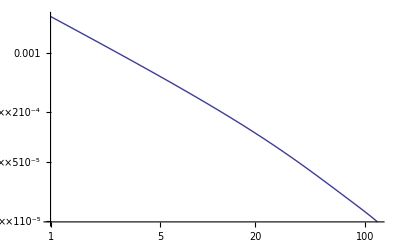

```mathematica
LogLogPlot[{dndeππγSimplified}/.{mx->200.,mpi->140.,Ecm->400.1,egam->eg,mv->1.,qe->√(4π/137.)},{eg,1,400-2*140}]
```

### Write to python file

```mathematica
FortranForm[dndeππγSimplified/.Ecm->Q]>>(pyDir<>"dnde_pipig.py");
```

### Fully simplified spectrum

```mathematica
(2α)/(π Egam(1-4 rπ^2)^(3/2))(-(1-x(1+x)-4 rπ^2(1-x))√(1-(4 rπ^2)/(1-x))+2(1-4 rπ^2)(1+x-2 rπ^2)ArcTanh[√(1-(4 rπ^2)/(1-x))])
```

## χ̄ χ→π^+ π^- π^0

It turns out that ℳ_(V→π^0 π^0 π^0)=0

```mathematica
threeMesonFSs={(*{stateη,stateη,stateη},
{stateη,statek0,statek0bar},
{stateη,statekp,statekm},
{stateη,stateη,stateπ0},
{statek0,statek0bar,stateπ0},
{statekp,statekm,stateπ0},
{stateη,stateπ0,stateπ0},
{statek0bar,statekp,stateπm},
{statek0,statekm,stateπp},
{stateη,stateπp,stateπm},*)
{stateπ0,stateπp,stateπm}};
```

Compute ((ℳ_(V^*→π^0 π^+π^-))^μ((ℳ_(V^*→π^0 π^+π^-))^ν))^*

```mathematica
ClearScalarProducts[];

ampSquaredxbarxtoπ0ππ=Module[{fs,diags,amp,ampSquared},
fs={stateπ0,stateπp,stateπm};

ClearScalarProducts[];
SP[p1,p1]=mpi0^2;
SP[p2,p2]=mpi^2;
SP[p3,p3]=mpi^2;

diags=genDiags[{statev},fs];
(*Paint[diags,ColumnsXRows->1,ImageSize->{200,200}];*)

amp=createAmp[diags,{P},{p1,p2,p3},{μ,α,ρ,σ},True]//substituteUnstableVPropagator[#,{p1,p2,p3}]&//PropagatorDenominatorExplicit//dropExtraVs;
(* Replace the ϵ symbol *)
amp=amp/.{FALeviCivita->Eps,FAFourVector->Momentum};

ampSquared=amp*ComplexConjugate[amp/.{μ->ν,α->β,ρ->λ,σ->δ}];

ampSquared//Limit[#,GaugeXi[Vec]->Infinity]&//Simplify
]
```

((gvdd+gvuu)^2 ϵ^(-OverBar[p1]-OverBar[p2]-OverBar[p3]μ) ϵ^(-OverBar[p1]-OverBar[p2]-OverBar[p3]ν))/(16 π^4 fpi^6)

Check that P_μ dotted with X^μν=∫dΠ_LIPS∑_(γ pols.) ((ℳ_(V^*→π^0 π^+π^-))^μ((ℳ_(V^*→π^0 π^+π^-))^ν))^* gives zero, where P is the V’s momentum:

```mathematica
Xμνπ0ππ=ampSquaredxbarxtoπ0ππ;
Xμνπ0ππ FV[P,μ]/.P->p1+p2+p3//Contract//ScalarProductExpand//Simplify
```

0

We therefore can write X^μν=(P^μ P^ν-P^2 g^μν)X(E_CM^2), where P^2=E_CM^2. This means the total cross section is given by
	σ=1/(2 E_CM^2 √(1-4m_x^2/E_CM^2))L^μα D_μν(D^*)_αβ X^νβ=1/((E_CM^2-m_V^2)^2)L^μν X_μν,
where D_μν is the V propagator, L^μν=1/4∑_(x,x̄ spins) ((ℳ_(x̄ x→V^*))^μ((ℳ_(x̄ x→V^*))^ν))^*, and I made use of the fact that P_μ L^μν=0:

```mathematica
setDMSPs[];

Lμν=FCI[FV[px,μ]FV[pxbar,ν]+FV[px,ν]FV[pxbar,μ]-1/2 Ecm^2 MT[μ,ν]];

Contract[FV[px+pxbar,μ]Lμν]//ScalarProductExpand//Simplify
```

0

Therefore the cross section is given by
	σ=1/(2 E_CM^2 √(1-4m_x^2/E_CM^2))1/((P^2-m_V^2)^2)(-E_CM^2/3)g^μν X_μν(E_CM^2).

```mathematica
(* Set Mandelstam variables *)
SP[p1,p2]=s/2-mpi^2;
SP[p1,p3]=(t-mpi^2)/2;
SP[p2,p3]=(u-mpi^2)/2;

dσπ0ππ=gvxx^2 xSecPrefactor[mx]/((Ecm^2-mv^2)^2+(mv widthv)^2)(-Ecm^2/3)(-MT[μ,ν]Xμνπ0ππ//Contract//ScalarProductExpand)/.u->2 mpi^2+Ecm^2-s-t//Simplify;
```

Finally, dσππγ must be integrated over 3-body phase space to give the spectrum
	σ=∫(ds dt)/(16 (E_CM^2(2π))^3)dσπ^0 ππ
Perform t integral:

```mathematica
Integrate[1/(16 Ecm^2(2π)^3)dσπ0ππ,t];

((%/.t->integrationBoundsT[s,mpi0,mpi,mpi,Ecm]⟦1⟧)-(%/.t->integrationBoundsT[s,mpi0,mpi,mpi,Ecm]⟦2⟧));
dσπ0ππTIntegrated=%//Simplify;
```

Numerically integrate over s

```mathematica
σπ0ππNumeric[mX_]:=If[2mX>3 140,
NIntegrate[dσπ0ππTIntegrated/.{s->ss,Ecm->2mx(1+1/2 10^-6),mpi0->135.,mpi->135.,mv->1.,gvuu->1,gvdd->1,fpi->93.,gvxx->1}/.mx->mX,{ss,4 140.^2,(2(1+1/2 10^-6)mX-140.)^2}],
0]
```

```mathematica
Module[{},
(dσπ0ππTIntegrated/.Ecm->Q)/.{widthv->1., s->0.5(smax+smin),gvuu->1.,gvdd->1.,gvxx->1.,fpi->92.2138,mv->1.}/.{smin->4 mpi^2,smax->(Q-mpi0)^2}/.{Q->2mx(1.+0.5 10^-6)}/.{mpi0->134.9766,mpi->139.57018,mx->1000.}
]
```

1.99666×10^-12

Save the result

```mathematica
dσπ0ππTIntegrated/.Ecm->Q//FortranForm>>(pyDir<>"xsec_t_integrated_xx_v_pi0pipi.py")
```

## χ̄ χ→ℓ̄ ℓ

```mathematica
ampSquaredxbarxtolbarl=Module[{fs,diags,amp,ampSquared},
fs={statelbar,statel};

ClearScalarProducts[];
setTwoBodyFSSPs[ml];

diags=genDiags[{statexbar,statex},fs];
(*Paint[diags,ColumnsXRows->{1,1}];*)

amp=createAmp[diags,{pxbar,px},{p1,p2},{μ,ν}]//substituteUnstableVPropagator[#,{p1,p2}]&//PropagatorDenominatorExplicit;

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]];
ampSquared=ampSquared//FermionSpinSum[#,ExtraFactor->1/4]&//ReplaceAll[#,DiracTrace->Tr]&//Contract;
ampSquared/.u->2(ml^2+mx^2)-s-t//Simplify
]
```

(2 gvll^2 gvxx^2 (2 Ecm^2 ml^2+2 ml^4+ml^2 (4 mx^2-2 s-4 t)+2 mx^4-4 mx^2 t+s^2+2 s t+2 t^2))/(mv^4+mv^2 (widthv^2-2 s)+s^2)

```mathematica
xSecxbarxtolbarl=getXSec[ampSquaredxbarxtolbarl,mx,ml,ml]/.s->Ecm^2//Simplify[#,Assumptions->{Ecm>ml,Ecm^2>ml^2}]&
```

(gvll^2 gvxx^2 √(Ecm^2-4 ml^2) (Ecm^2+2 ml^2) (Ecm^2+2 mx^2))/(12 π Ecm^2 √(Ecm^2-4 mx^2) (Ecm^4-2 Ecm^2 mv^2+mv^4+mv^2 widthv^2))

```mathematica
(*FortranForm[xSecxbarxtolbarl]>>(pyDir<>"xsec_xx_v_ll.py")*)
```

## χ̄ χ→ℓ̄ ℓγ

Fully simplified spectrum:

```mathematica
(2α)/(Egam π(1-4 rl^2)^(1/2)(1+2rl))((2-x(2-x)+4(1-x)rl^2)√(1-(4 rl^2)/(1-x))+2(2-x(2-x)-4 rl^2(x+2 rl^2))ArcTanh[√(1-(4 rl^2)/(1-x))])
```

## χ̄ χ→V V

```mathematica
ClearScalarProducts[];

ampSquaredxbarxtovv=Module[{fs,diags,amp,ampSquared},
fs={statev,statev};

ClearScalarProducts[];
setTwoBodyFSSPs[mv];

diags=genDiags[{statexbar,statex},fs];
amp=createAmp[diags,{pxbar,px},{p1,p2},{μ,ν}]//PropagatorDenominatorExplicit;

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]];
ampSquared=ampSquared//FermionSpinSum[#,ExtraFactor->1/4]&//ReplaceAll[#,DiracTrace->Tr]&;
ampSquared=ampSquared//DoPolarizationSums[#,p1]&//DoPolarizationSums[#,p2]&;
ampSquared/.u->2(mv^2+mx^2)-s-t/.s->Ecm^2//Simplify
]
```

-(2 gvxx^4 (Ecm^6 (t-mx^2)+Ecm^4 (mv^4+mv^2 (6 mx^2-2 t)+3 mx^4-2 mx^2 t+3 t^2)-2 Ecm^2 (2 mv^6+mv^4 (11 mx^2-3 t)+4 mv^2 (2 mx^4-mx^2 t+t^2)-2 t (mx^2-t)^2)+2 (2 mv^8+2 mv^6 (7 mx^2-3 t)+mv^4 (15 mx^4-14 mx^2 t+7 t^2)+4 mv^2 (mx^2-t)^3+(mx^2-t)^4)))/((mx^2-t)^2 (Ecm^2-2 mv^2-mx^2+t)^2)

### Simplify by hand to deal with the logs

```mathematica
getXSecTIntegral[ampSquaredxbarxtovv,mx,mv]/.s->Ecm^2//Simplify//StandardForm
```

```mathematica
xSecxbarxtovv=1/(16 Ecm^2 √(Ecm^2-4 mx^2) π)gvxx^4 √(Ecm^2-4 mv^2) (-2 √((Ecm^2-4 mv^2) (Ecm^2-4 mx^2))-(2 √((Ecm^2-4 mv^2) (Ecm^2-4 mx^2)) (mv^2+2 mx^2)^2)/(mv^4+Ecm^2 mx^2-4 mv^2 mx^2)+(Ecm^4+4 mv^4+4 Ecm^2 mx^2-8 mv^2 mx^2-8 mx^4)/(Ecm^2-2 mv^2)Log[((Ecm^2-2 mv^2+√((Ecm^2-4 mv^2) (Ecm^2-4 mx^2)))^2)/((-Ecm^2+2 mv^2+√((Ecm^2-4 mv^2) (Ecm^2-4 mx^2)))^2)]);
```

### Save the cross section

```mathematica
(*FortranForm[xSecxbarxtovv/.Ecm->Q]>>(pyDir<>"xsec_xx_vv.py")*)
```

## Amplitudes with resonances

```mathematica
otherFSs={{statek0,statek0bar,stateω},
{statekp,statekm,stateω},
{stateπp,stateπm,stateρ},
{statekp,statekm,stateρ},
{statek0,statek0bar,stateρ}};
```

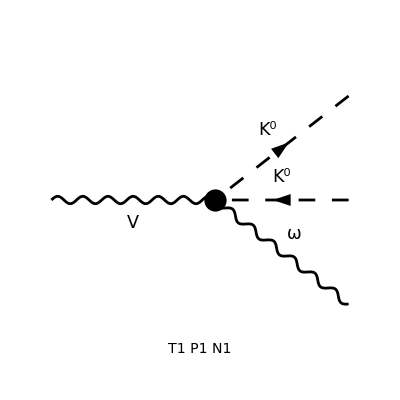

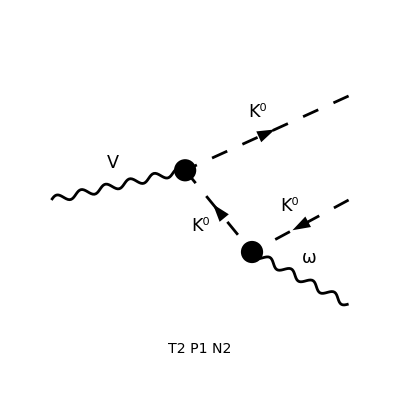

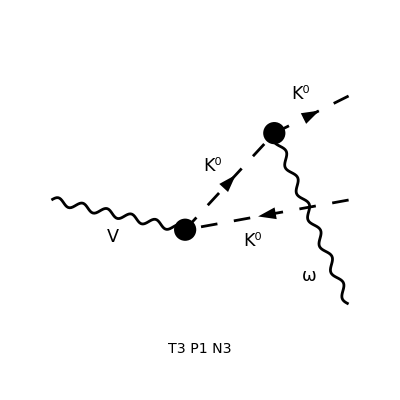

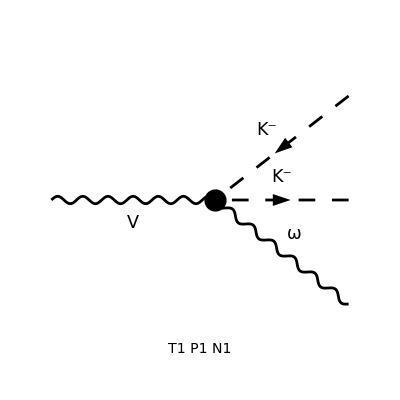

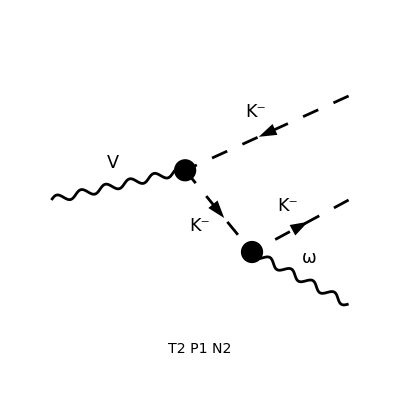

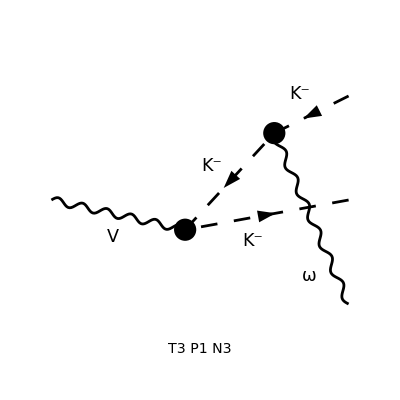

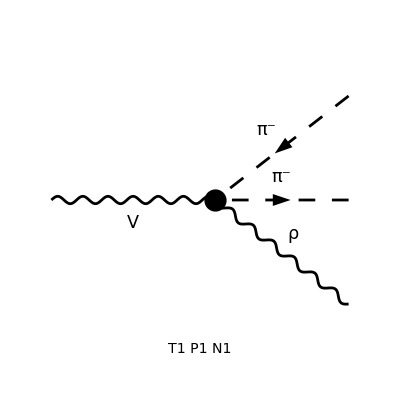

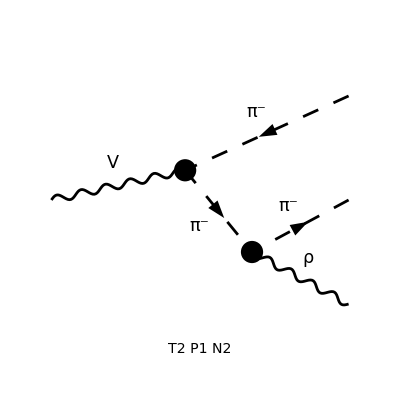

```mathematica
For[i=1,i≤Length[otherFSs],i++,
Module[{diags,len},
diags=genDiags[{statev},otherFSs⟦i⟧];

If[Length[diags]≠0,Paint[diags,ColumnsXRows->1,ImageSize->{200,200}];
];
]
]
```

# V→A

## V→π^+ π^-

```mathematica
ClearScalarProducts[];

widthvtoππ=Module[{fs,diags,amp,ampSquared},
fs={stateπp,stateπm};

ClearScalarProducts[];
SP[p1,p1]=mpi^2;
SP[p2,p2]=mpi^2;
SP[p1,p2]=mv^2/2-mpi^2;
SP[P,P]=mv^2;

diags=genDiags[{statev},fs];
amp=createAmp[diags,{P},{p1,p2},{μ,ν}];

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]];
ampSquared=ampSquared//DoPolarizationSums[#,P]&;
widthFactor[mpi]ampSquared/.{P->p1+p2}//ScalarProductExpand//Simplify
]
```

((gvdd-gvuu)^2 (mv^2-4 mpi^2)^(3/2))/(16 π mv^2)

```mathematica
FortranForm[widthvtoππ]>>(pyDir<>"width_v_pipi.py")
```

## V→π^0 γ

```mathematica
ClearScalarProducts[];

widthvtoπ0γ=Module[{fs,diags,amp,ampSquared},
fs={stateπ0,stateγ};

ClearScalarProducts[];
SP[p1,p1]=mpi^2;
SP[k,k]=0;
SP[p1,k]=(mv^2-mpi0^2)/2;
SP[P,P]=mv^2;

diags=genDiags[{statev},fs];
amp=createAmp[diags,{P},{p1,k},{μ,ν}];
(* Replace the ϵ symbol *)
amp=amp/.{FALeviCivita->Eps,FAFourVector->Momentum};

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]];
ampSquared=ampSquared//DoPolarizationSums[#,k,0]&//DoPolarizationSums[#,P]&;
widthFactor[mpi0,0]ampSquared/.{P->p1+k}//ScalarProductExpand//Simplify
]
```

(qe^2 (gvdd+2 gvuu)^2 (mv^2-mpi0^2) (4 mpi^4 mv^2+mpi^2 (mpi0^4-12 mpi0^2 mv^2+13 mv^4)-mpi0^6+12 mpi0^4 mv^2-21 mpi0^2 mv^4+4 mv^6))/(18432 π^5 fpi^2 mv^5)

```mathematica
FortranForm[widthvtoπ0γ]>>(pyDir<>"width_v_pi0g.py")
```

## V→ℓ̄ ℓ

```mathematica
widthvtolbarl=Module[{fs,diags,amp,ampSquared},
fs={statelbar,statel};

ClearScalarProducts[];
SP[P,P]=mv^2;
SP[p1,p1]=ml^2;
SP[p1,p2]=mv^2/2-ml^2;
SP[p2,p2]=ml^2;

diags=genDiags[{statev},fs];
(*Paint[diags,ColumnsXRows->{1,1}];*)

amp=createAmp[diags,{P},{p1,p2},{μ,ν}]//PropagatorDenominatorExplicit;

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]];
ampSquared=ampSquared//FermionSpinSum//ReplaceAll[#,DiracTrace->Tr]&//Contract//DoPolarizationSums[#,P]&;
widthFactor[ml]ampSquared/.P->p1+p2//ScalarProductExpand//Simplify
]
```

(gvll^2 √(mv^2-4 ml^2) (2 ml^2+mv^2))/(4 π mv^2)

```mathematica
FortranForm[widthvtolbarl]>>(pyDir<>"width_v_lbarl.py")
```

## V→χ̄ χ

```mathematica
widthvtoxbarx=Module[{fs,diags,amp,ampSquared},
fs={statexbar,statex};

ClearScalarProducts[];
SP[P,P]=mv^2;
SP[p1,p1]=mx^2;
SP[p1,p2]=mv^2/2-mx^2;
SP[p2,p2]=mx^2;

diags=genDiags[{statev},fs];
(*Paint[diags,ColumnsXRows->{1,1}];*)

amp=createAmp[diags,{P},{p1,p2},{μ,ν}]//PropagatorDenominatorExplicit;

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]];
ampSquared=ampSquared//FermionSpinSum//ReplaceAll[#,DiracTrace->Tr]&//Contract//DoPolarizationSums[#,P]&;
widthFactor[mx]ampSquared/.P->p1+p2//ScalarProductExpand//Simplify
]
```

(gvxx^2 √(mv^2-4 mx^2) (mv^2+2 mx^2))/(4 π mv^2)

```mathematica
FortranForm[widthvtoxbarx]>>(pyDir<>"width_v_xbarx.py")
```

## V→π^+π^-π^0

```mathematica
widthvtoπππ0=Module[{fs,diags,amp,ampSquared},
fs={stateπ0,stateπp,stateπm};

ClearScalarProducts[];
SP[p1,p1]=mpi0^2;
SP[p2,p2]=mpi^2;
SP[p3,p3]=mpi^2;
SP[P,P]=mv^2;

diags=genDiags[{statev},fs];
(*Paint[diags];*)
amp=createAmp[diags,{P},{p1,p2,p3},{μ,ν}]//PropagatorDenominatorExplicit//dropExtraVs;
(* Replace the ϵ symbol *)
amp=amp/.{FALeviCivita->Eps,FAFourVector->Momentum};

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]];
ampSquared=ampSquared//DoPolarizationSums[#,P]&;
ampSquared//Simplify
]
```

1/(16 π^4 fpi^6 mv^2)(gvdd+gvuu)^2 ((P̄·OverBar[p1])^2 (mpi^4-(OverBar[p2]·OverBar[p3])^2)+(P̄·OverBar[p3])^2 (mpi^2 mpi0^2-(OverBar[p1]·OverBar[p2])^2)+(P̄·OverBar[p2])^2 (mpi^2 mpi0^2-(OverBar[p1]·OverBar[p3])^2)-2 (P̄·OverBar[p1]) ((P̄·OverBar[p3]) (mpi^2 (OverBar[p1]·OverBar[p3])-(OverBar[p1]·OverBar[p2]) (OverBar[p2]·OverBar[p3]))+(P̄·OverBar[p2]) (mpi^2 (OverBar[p1]·OverBar[p2])-(OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p3])))+2 (P̄·OverBar[p2]) (P̄·OverBar[p3]) ((OverBar[p1]·OverBar[p2]) (OverBar[p1]·OverBar[p3])-mpi0^2 (OverBar[p2]·OverBar[p3])))

## Scratch

```mathematica
Solve[k+Sqrt[k^2+mpi0^2]==cme,k]//StandardForm
```

{{k→(cme^2-mpi0^2)/(2 cme)}}

```mathematica
√(((cme^2-mpi0^2)/(2 cme))^2+mpi0^2)//FullSimplify[#,Assumptions->{mpi>0,cme>0,mpi^2>0,cme^2>0}]&
```

(√((cme^2+mpi0^2)^2))/(2 cme)

```mathematica
Solve[4 mpi^2==(Q-k)^2-k^2,k]
```

{{k→(Q^2-4 mpi^2)/(2 Q)}}

```mathematica
ampSquaredxbarxtoππ=Module[{fs,diags,amp,ampSquared},
fs={stateγ,stateγ};

ClearScalarProducts[];

diags=genDiags[{statexbar,statex},fs];
Paint[diags]
]
```

Paint::nolevel: Warning: Level TraditionalForm`Particles is not contained in this insertion.

FeynArtsGraphics({\chi,\chi}→{\gamma,\gamma})()

FeynArtsGraphics({\chi,\chi}→{\gamma,\gamma})()

# Scratch

### LATEX expressions

```mathematica
xSecxbarxtolbarl/.{Ecm->Q,mx->rx Q,ml->rl Q}//FullSimplify[#,Assumptions->Q>0]&//TeXForm
```

\frac{\text{gvll}^2 \text{gvxx}^2 Q^2 \sqrt{1-4 \text{rl}^2} \left(2
   \text{rl}^2+1\right) \left(2 \text{rx}^2+1\right)}{12 \pi  \sqrt{1-4
   \text{rx}^2} \left(\left(\text{mv}^2-Q^2\right)^2+\text{mv}^2
   \text{widthv}^2\right)}

```mathematica
xSecxbarxtoπ0γ/.{Ecm->Q,mx->rx Q,mpi0->rpi0 Q}//FullSimplify[#,Assumptions->Q>0]&//TeXForm
```

-\frac{\text{gvxx}^2 Q^4 \text{qe}^2 \left(\text{rpi0}^2-1\right)^3 \left(2
   \text{rx}^2+1\right) (\text{gvdd}+2 \text{gvuu})^2}{13824 \pi ^5
   \text{fpi}^2 \sqrt{1-4 \text{rx}^2}
   \left(\left(\text{mv}^2-Q^2\right)^2+\text{mv}^2 \text{widthv}^2\right)}

```mathematica
xSecxbarxtoππ/.{Ecm->Q,mx->rx Q,mpi->rpi Q}//FullSimplify[#,Assumptions->Q>0]&
```

(gvxx^2 Q^2 (1-4 rpi^2)^(3/2) (2 rx^2+1) (gvdd-gvuu)^2)/(48 π √(1-4 rx^2) ((mv^2-Q^2)^2+mv^2 widthv^2))

```mathematica
xSecxbarxtovv/.{Ecm->Q,mx->rx Q,mv->rv Q}//FullSimplify[#,Assumptions->Q>0]&
```

1/(16 π √(1-4 rx^2))gvxx^4 √(1-4 rv^2) (((-4 rv^4+4 (2 rv^2-1) rx^2+8 rx^4-1) log(((√(Q^4 (4 rv^2-1) (4 rx^2-1))+Q^2 (1-2 rv^2))^2)/(Q^4 (√((4 rv^2-1) (4 rx^2-1))+2 rv^2-1)^2)))/(2 rv^2-1)-(2 √((4 rv^2-1) (4 rx^2-1)) (2 rv^4+4 rx^4+rx^2))/(rv^4-4 rv^2 rx^2+rx^2))

```mathematica
(gvxx^4 √(1-4 rv^2) ((2 √((1-4 rv^2) (1-4 rx^2)) (2 rv^4+rx^2+4 rx^4))/(4 rv^2 rx^2-rv^4-rx^2)+((1+4 rv^4+4 (1-2 rv^2) rx^2-8 rx^4) Log[(( 1-2 rv^2+√((1-4 rv^2) (1-4 rx^2)))^2)/((1-2 rv^2-√((1-4 rv^2) (1-4 rx^2)))^2)])/(1-2 rv^2)))/(16 π √(1-4 rx^2))//TeXForm
```

\frac{\text{gvxx}^4 \sqrt{1-4 \text{rv}^2} \left(\frac{2 \sqrt{\left(1-4 \text{rv}^2\right) \left(1-4 \text{rx}^2\right)} \left(2 \text{rv}^4+4
   \text{rx}^4+\text{rx}^2\right)}{-\text{rv}^4+4 \text{rv}^2 \text{rx}^2-\text{rx}^2}+\frac{\left(4 \text{rv}^4+4 \left(1-2 \text{rv}^2\right) \text{rx}^2-8
   \text{rx}^4+1\right) \log \left(\frac{\left(\sqrt{\left(1-4 \text{rv}^2\right) \left(1-4 \text{rx}^2\right)}-2 \text{rv}^2+1\right)^2}{\left(-\sqrt{\left(1-4
   \text{rv}^2\right) \left(1-4 \text{rx}^2\right)}-2 \text{rv}^2+1\right)^2}\right)}{1-2 \text{rv}^2}\right)}{16 \pi  \sqrt{1-4 \text{rx}^2}}

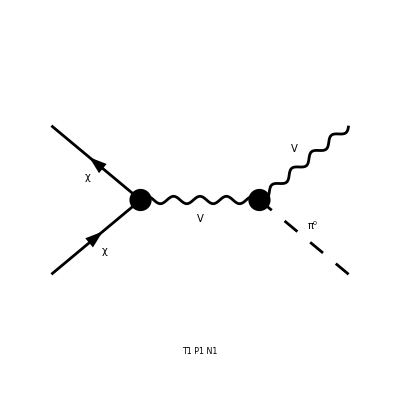

FeynArtsGraphics({\chi,\chi}→{V,ComposedChar(\pi,Null,0)})(([T1 P1 N1] | Null | Null
Null | Null | Null
Null | Null | Null))

Paint::nolevel: Warning: Level TraditionalForm`Particles is not contained in this insertion.

FeynArtsGraphics({\chi,\chi}→{ComposedChar(K,Null,0),\gamma})()

FeynArtsGraphics({\chi,\chi}→{ComposedChar(K,Null,0),\gamma})()

```mathematica
ClearScalarProducts[];

Module[{fs,diags,amp,ampSquared},
fs={statev,stateπ0};

diags=genDiags[{statexbar,statex},fs];
Paint[diags]
]
```